# Schwinger Effect in Electric Field

### For a particle in an electric field, the Lagrangian is:

```mathematica
L=m/(2n)(-t'[T]^2+x'[T]^2)-(m n)/2+(k t'[T]x[T])
```

-(m n)/2+k x[T] t'[T]+(m (-t'[T]^2+x'[T]^2))/(2 n)

### Let’s test all the derivatives and see if we get the right results:

#### Partials wrt x

```mathematica
D[L,x[T]]
D[L,x'[T]]
```

k t'[T]

(m x'[T])/n

```mathematica
D[D[L,x'[T]],T]
```

(m x''[T])/n

#### Partials wrt t

```mathematica
D[L,t[T]]
D[L,t'[T]]
```

0

k x[T]-(m t'[T])/n

```mathematica
D[D[L,t'[T]],T]
```

k x'[T]-(m t''[T])/n

Yes we do!

### Find the equations of motion:

```mathematica
D[D[L,x'[T]],T]-D[L,x[T]]==0
```

-k t'[T]+(m x''[T])/n==0

```mathematica
D[D[L,t'[T]],T]-D[L,t[T]]==0
```

k x'[T]-(m t''[T])/n==0

```mathematica
D[D[D[L,t'[T]],T]-D[L,t[T]],T]==0
```

k x''[T]-(m t^(3)[T])/n==0

NOT SURE WHY WE DID THIS ?? ^

### Solve the equation of motion to get x(T) and t(T):

```mathematica
soltx=DSolve[{- k t'[T]+(m x''[T])/n==0,k x'[T]-(m t''[T])/n==0, x[0]==xa,x[1]==xb,t[0]==ta,t[1]==tb},{t,x},T]
```

{{t→Function[{T},-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (-ⅇ^((k n)/m) ta+ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n)/m+(k n T)/m) ta+ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb-ⅇ^((k n)/m+(k n T)/m) tb+ⅇ^((k n)/m) xa-ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n)/m+(k n T)/m) xa-ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb+ⅇ^((k n)/m+(k n T)/m) xb)],x→Function[{T},-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (ⅇ^((k n)/m) ta-ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n)/m+(k n T)/m) ta-ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb+ⅇ^((k n)/m+(k n T)/m) tb-ⅇ^((k n)/m) xa+ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n)/m+(k n T)/m) xa+ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb-ⅇ^((k n)/m+(k n T)/m) xb)]}}

```mathematica
Factor[FullSimplify[t[T]/.soltx[[1]]/.{xa->0,ta->0},Trig->True]] (* Simplify the t solution *)
```

Csch[(k n)/(2 m)] (tb Cosh[(k n (-1+T))/(2 m)]+xb Sinh[(k n (-1+T))/(2 m)]) Sinh[(k n T)/(2 m)]

```mathematica
Factor[FullSimplify[x[T]/.soltx[[1]]/.{xa->0,ta->0},Trig->True]] (* Simplify the x solution *)
```

Csch[(k n)/(2 m)] (xb Cosh[(k n (-1+T))/(2 m)]+tb Sinh[(k n (-1+T))/(2 m)]) Sinh[(k n T)/(2 m)]

### Trajectory plots:

```mathematica
Clear[xa,xb,ta, tb,m, k, n];
```

```mathematica
par={xa->0,xb->4,ta-> 0, tb -> 6,m->1,n->1, k->2};
par2={xa->0,xb->4,ta-> 0, tb -> 6,m->1,n->1, k->3};(* Different parameters *)
```

#### Simplified expressions for t :

```mathematica
f=t[T]/.soltx⟦1⟧/.par
f2=t[T]/.soltx⟦1⟧/.par2
```

-(ⅇ^(-2 T) (2 ⅇ^2+10 ⅇ^(2 T)-10 ⅇ^(4 T)-2 ⅇ^(2+2 T)))/(2 (-1+ⅇ^2))

-(ⅇ^(-3 T) (2 ⅇ^3+10 ⅇ^(3 T)-10 ⅇ^(6 T)-2 ⅇ^(3+3 T)))/(2 (-1+ⅇ^3))

#### Simplified expressions for x :

```mathematica
g=x[T]/.soltx⟦1⟧/.par
g2=x[T]/.soltx⟦1⟧/.par2
```

-(ⅇ^(-2 T) (-2 ⅇ^2+10 ⅇ^(2 T)-10 ⅇ^(4 T)+2 ⅇ^(2+2 T)))/(2 (-1+ⅇ^2))

-(ⅇ^(-3 T) (-2 ⅇ^3+10 ⅇ^(3 T)-10 ⅇ^(6 T)+2 ⅇ^(3+3 T)))/(2 (-1+ⅇ^3))

#### Plots of x and t wrt to T :

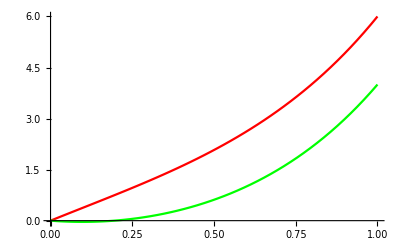

```mathematica
Plot[{f,g},{T,0,1},PlotStyle->{Red,Green}]
```

#### Trajectory for particle in electric field (t versus x) :

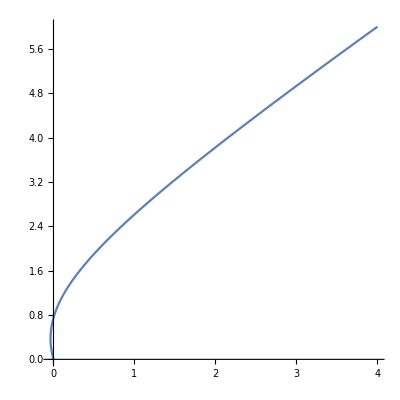

```mathematica
ParametricPlot[{g,f},{T,0,1},AspectRatio->1]
```

#### Attempt at Manipulate function:

```mathematica
Clear[xm]
```

```mathematica
(* Variables storing expressions for x and t *)
xm= x[T]/.soltx⟦1⟧
```

-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (ⅇ^((k n)/m) ta-ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n)/m+(k n T)/m) ta-ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb+ⅇ^((k n)/m+(k n T)/m) tb-ⅇ^((k n)/m) xa+ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n)/m+(k n T)/m) xa+ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb-ⅇ^((k n)/m+(k n T)/m) xb)

```mathematica
(*rep={xa->xaa,xb->xbb,ta->taa,tb->tbb,m->mm,n->nn,k->kk};*)
```

```mathematica
Clear[tm]
```

```mathematica
tm=t[T]/.soltx⟦1⟧
```

-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (-ⅇ^((k n)/m) ta+ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n)/m+(k n T)/m) ta+ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb-ⅇ^((k n)/m+(k n T)/m) tb+ⅇ^((k n)/m) xa-ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n)/m+(k n T)/m) xa-ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb+ⅇ^((k n)/m+(k n T)/m) xb)

```mathematica
Manipulate[ 
Grid[{
ParametricPlot[{-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (ⅇ^((k n)/m) ta-ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n)/m+(k n T)/m) ta-ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb+ⅇ^((k n)/m+(k n T)/m) tb-ⅇ^((k n)/m) xa+ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n)/m+(k n T)/m) xa+ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb-ⅇ^((k n)/m+(k n T)/m) xb),-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (-ⅇ^((k n)/m) ta+ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n)/m+(k n T)/m) ta+ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb-ⅇ^((k n)/m+(k n T)/m) tb+ⅇ^((k n)/m) xa-ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n)/m+(k n T)/m) xa-ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb+ⅇ^((k n)/m+(k n T)/m) xb)},{T,0,1},AspectRatio->1,ImageSize->500,PlotRange->All],
ParametricPlot[{-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (ⅇ^((k n)/m) ta-ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n)/m+(k n T)/m) ta-ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb+ⅇ^((k n)/m+(k n T)/m) tb-ⅇ^((k n)/m) xa+ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n)/m+(k n T)/m) xa+ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb-ⅇ^((k n)/m+(k n T)/m) xb),-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (-ⅇ^((k n)/m) ta+ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n)/m+(k n T)/m) ta+ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb-ⅇ^((k n)/m+(k n T)/m) tb+ⅇ^((k n)/m) xa-ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n)/m+(k n T)/m) xa-ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb+ⅇ^((k n)/m+(k n T)/m) xb)},{T,0,1},AspectRatio->1,ImageSize->500,PlotRange->All]
}],
{xa,0,100},
{{xb,20},0,100},
{ta,0,100},
{tb,0,100},
{{m,4},0.0001,100},
{{n,6},0.0001,100},
{{k,3},0.000001,5}]
```

### Find the classical action:

```mathematica
LL =Simplify[L/.soltx[[1]]] (* Storing the Lagrangian with the solution plugged in *)
```

1/(4 (-1+ⅇ^((k n)/m))^2 m)ⅇ^(-(2 k n T)/m) n (-2 ⅇ^((2 k n T)/m) m^2-2 ⅇ^((2 k n (1+T))/m) m^2+4 ⅇ^((k n (1+2 T))/m) m^2+ⅇ^((4 k n T)/m) k^2 (ta-tb+xa-xb)^2+ⅇ^((2 k n)/m) k^2 (ta-tb-xa+xb)^2-ⅇ^((k n (1+3 T))/m) k^2 (ta^2-2 ta tb+tb^2+2 ta xa-2 tb xa+xa^2-xb^2)-ⅇ^((k n (1+T))/m) k^2 (ta^2+tb^2+2 tb xa+xa^2-2 ta (tb+xa)-xb^2)-ⅇ^((k n (2+T))/m) k^2 (ta^2-2 ta tb+tb^2-xa^2+2 ta xb-2 tb xb+xb^2)-ⅇ^((3 k n T)/m) k^2 (ta^2+tb^2-xa^2+2 tb xb+xb^2-2 ta (tb+xb)))

```mathematica
Scl=Simplify[Integrate[LL,{T,0,1}]] (* Integrating the Lagrangian over T to get the classical action *)
```

1/4 (-2 (m n+k (ta-tb) (xa+xb))-k (ta-tb+xa-xb) (ta-tb-xa+xb) Coth[(k n)/(2 m)])

```mathematica
Scl/.{xa->0,ta->0} (* Using simplified initial values for x and t *)
```

1/4 (-2 (m n-k tb xb)-k (-tb-xb) (-tb+xb) Coth[(k n)/(2 m)])

### Evaluate the prefactor

This is not its derivation but just an evaluation where the prefactor is 1/Sqrt(Det[mx]) where the mx is a matrix with entries given below by Scl1, Scl2, Scl3, and Scl4.

```mathematica
Scl1=D[Scl,xa,xb] (* Evaluating each entry in the matrix *)
```

-1/2 k Coth[(k n)/(2 m)]

```mathematica
Scl2 = D[Scl,xa,tb]
```

k/2

```mathematica
Scl3 = D[Scl,ta,xb]
```

-k/2

```mathematica
Scl4 = D[Scl,ta,tb]
```

1/2 k Coth[(k n)/(2 m)]

```mathematica
Mx=({{Scl1, Scl2}, {Scl3, Scl4}}) (* Plugging in all the evaluated entries *)
```

{{-1/2 k Coth[(k n)/(2 m)],k/2},{-k/2,1/2 k Coth[(k n)/(2 m)]}}

```mathematica
Pref=FullSimplify[1/(√Det[Mx])] (* Evaluating and simplifying the full prefactor *)
```

2/(√(-k^2 Csch[(k n)/(2 m)]^2))

### Figure out how to find the kernel!

The kernel is ultimately an integral over N from 0 to ∞ of the integrand below (stored as Int):

```mathematica
Int = FullSimplify[Pref*Exp[ⅈ Scl/ℏ]]
```

(2 ⅇ^(-(ⅈ (2 m n+2 k (ta-tb) (xa+xb)+k (ta-tb+xa-xb) (ta-tb-xa+xb) Coth[(k n)/(2 m)]))/(4 ℏ)))/(√(-k^2 Csch[(k n)/(2 m)]^2))

However, this integral is extremely difficult (or impossible?) to solve analytically, so we need to use an approximation.

Specifically, we will use a saddle point approximation. That involves allowing N to be complex, and thus allowing the function (i.e. the integrand) to have dependence on complex N (introducing the complex plane). The original contour of the function in the complex plane is very much oscillatory, with an every increasing amplitude of oscillations, which is why it is so tough to solve the integral analytically.Using Cauchy’s theorem, we can deform the original oscillatory contour of the function, which would be a line integral in the 3D-space and restricted to real values of N, to any other “well-behaved” contour such that the contour does not pass over any undefined points (i.e. the function needs to be holomorphic), and the integral over this new contour would be the same as the original contour integral. To quote Wikipedia:  “...if two different paths connect the same two points, and a function is holomorphic everywhere in between the two paths, then the two path integrals of the function will be the same.” (More about holomorphic functions later?) 

Deforming the original path is helpful in the approximation process since the path can be deformed to pass through the highest stationary point/s, with other conditions satisfied of course, and then the path integral would be dominated by that stationary point (or points). It turns out that the only extrema possible in our case are saddle points, so we deform the path to pass through a saddle point (with steepest descent?). [https://www2.ph.ed.ac.uk/~dmarendu/MOMP/lecture05.pdf]

We have been talking about our oscillatory “function” as the whole integrand, but, ignoring the prefactor for now, truly what is relevant is the classical action, Scl, because when we set (d(Int))/dN=0 in order to find the extrema, we get (d(ⅈScl/ℏ))/dN e^(ⅈScl/ℏ)=0 , where the exponent term can’t go to 0, and ⅈ and ℏ are constants, so we know that the extrema are given by (d(Scl))/dN=0, thus the oscillatory function we are concerned with is just Scl.

```mathematica
(* Re[fullinteg/.{xa->0,xb->1,ta->0,tb->1,m->1,k->1,ℏ->1}]//FullSimplify *)
```

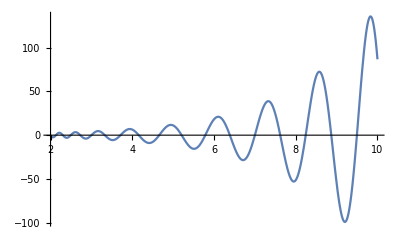

```mathematica
Plot[Re[Int/.{xa->0,xb->6,ta->0,tb->4,m->1,k->1,ℏ->0.1}],{n,2,10},PlotRange->All] (* Plot of the function showing oscillatory behavior *)
```

```mathematica
Soln = Solve[D[Scl, n]==0, n] (* Finding the extrema, where C[1] is a constant integer, so there are infinitely many solutions *)
```

{{n→ConditionalExpression[(2 m (-ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]+2 ⅈ π C[1]))/k,C[1]∈ℤ]},{n→ConditionalExpression[(2 m (ⅈ π-ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]+2 ⅈ π C[1]))/k,C[1]∈ℤ]},{n→ConditionalExpression[(2 m (ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]+2 ⅈ π C[1]))/k,C[1]∈ℤ]},{n→ConditionalExpression[(2 m (ⅈ π+ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]+2 ⅈ π C[1]))/k,C[1]∈ℤ]}}

```mathematica
Clear[Sp,Sp1,Sp2,Sp3,Sp4,Test,Test1,Pl1,Pl2]
Clear[Pl2]
```

```mathematica
Test1 = {xa->0,xb->6,ta-> 0, tb -> 4,m->1, k->1, C[1]->c1};
```

```mathematica
Sp0 = FullSimplify[Normal @ n/.Soln⟦1⟧/.Test1,c1∈Integers && c1∈Reals ]
```

2 ⅈ (2 c1 π-ArcSin[√5])

```mathematica
Sp11 = FullSimplify[Normal @n/.Soln⟦1⟧/.Test1,c1∈Integers&& c1∈Reals ]
```

2 ⅈ (2 c1 π-ArcSin[√5])

```mathematica
Sp22 = FullSimplify[Normal @n/.Soln⟦2⟧/.Test1,c1∈Integers&& c1∈Reals ]
```

ⅈ (π+4 c1 π+2 ArcCos[√5])

```mathematica
Sp33 = FullSimplify[Normal @n/.Soln⟦3⟧/.Test1,c1∈Integers&& c1∈Reals ]
```

2 ⅈ (2 c1 π+ArcSin[√5])

```mathematica
Sp44 = FullSimplify[Normal @n/.Soln⟦4⟧/.Test1,c1∈Integers&& c1∈Reals ]
```

2 ⅈ (π+2 c1 π+ArcSin[√5])

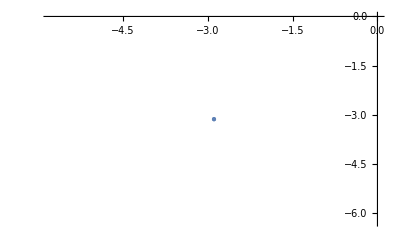

```mathematica
ListPlot[{{Re[Sp11]/.c1->0,Im[Sp11]/.c1->0}(*,{Re[Sp22],Im[Sp22]},{Re[Sp33],Im[Sp33]},{Re[Sp44],Im[Sp44]}*)},PlotStyle->PointSize[Large], PlotRange->All]
```

```mathematica
Manipulate[
 ListPlot[{{Re[Sp11]/.c1->cc,Im[Sp11]/.c1->cc}(*,{Re[Sp22],Im[Sp22]},{Re[Sp33],Im[Sp33]},{Re[Sp44],Im[Sp44]}*)},PlotStyle->PointSize[Large], PlotRange->All],
{{cc,0},-10,10, 1}
]
```

```mathematica
Test = {xa->0,xb->6,ta-> 0, tb -> 4,m->1, k->1,C[1]->-1};
```

```mathematica
Sp = FullSimplify[n/.Soln⟦1⟧/.Test]
```

-2 ⅈ (2 π+ArcSin[√5])

```mathematica
Sp1 = FullSimplify[n/.Soln⟦1⟧/.Test]
```

-2 ⅈ (2 π+ArcSin[√5])

```mathematica
Sp2 = FullSimplify[n/.Soln⟦2⟧/.Test]
```

-2 ⅈ (π+ArcSin[√5])

```mathematica
Sp3 = FullSimplify[n/.Soln⟦3⟧/.Test ]
```

-3 ⅈ π+2 ArcCosh[√5]

```mathematica
Sp4 = FullSimplify[n/.Soln⟦4⟧/.Test ]
```

-ⅈ (π+2 ArcCos[√5])

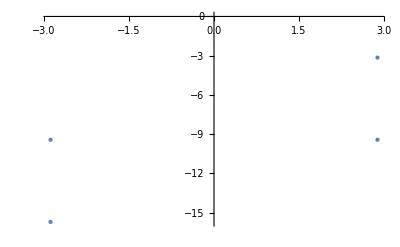

```mathematica
Pl1 = ListPlot[{{Re[Sp1],Im[Sp1]},{Re[Sp2],Im[Sp2]},{Re[Sp3],Im[Sp3]},{Re[Sp4],Im[Sp4]}},PlotStyle->PointSize[Large], PlotRange->All]
```

```mathematica
Int/.Test
```

(2 ⅇ^(-(ⅈ (-48+2 n-20 Coth[n/2]))/(4 ℏ)))/(√(-Csch[n/2]^2))

```mathematica
ReIm[Int/.Test/.{n->nr+ⅈ ni}//FullSimplify]
```

{2 Re[ⅇ^((ni-ⅈ (-24+nr)+10 Cot[1/2 (ni-ⅈ nr)])/(2 ℏ))/(√(Csc[1/2 (ni-ⅈ nr)]^2))],2 Im[ⅇ^((ni-ⅈ (-24+nr)+10 Cot[1/2 (ni-ⅈ nr)])/(2 ℏ))/(√(Csc[1/2 (ni-ⅈ nr)]^2))]}

```mathematica
Pl2 = ContourPlot[Re[ⅈ Scl/.Test/.{n->nr+ⅈ ni}],{nr, -10, 10},{ ni, -10, 10}, ColorFunction->"TemperatureMap", Contours->100]
```

-Graphics-

```mathematica
Replot=Show[Pl2,Pl1]
```

-Graphics-

```mathematica
Pl3 = ContourPlot[Im[ⅈ Scl/.Test/.{n->nr+ⅈ ni}],{nr, -10, 10},{ ni, -10, 10}, ColorFunction->"TemperatureMap", Contours->150]
```

-Graphics-

```mathematica
Implot=Show[Pl3,Pl1]
```

-Graphics-

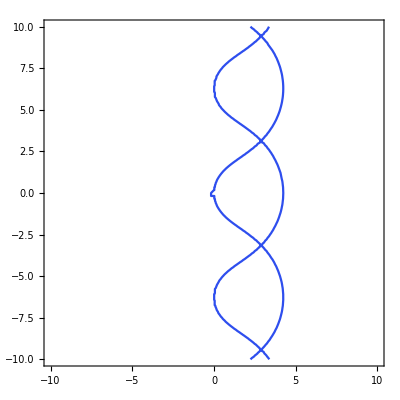

```mathematica
Pl4 = ContourPlot[Im[ⅈ Scl/.Test/.{n->nr+ⅈ ni}]==Im[ⅈ Scl/ⅇ^0/.Test/.{n->-ⅈ (π+2 ArcCos[√5])}],{nr, -10, 10},{ ni, -10, 10}, ColorFunction->"TemperatureMap", Contours->150]
```

```mathematica
Show[Pl2,Pl1,Pl4]
```

-Graphics-

```mathematica
(*Pl5 = ContourPlot[Re[ⅈ Scl/.Test/.{n->nr+ⅈ ni}]==Re[ⅈ Scl/ⅇ^0/.Test/.{n->-ⅈ (π+2 ArcCos[√5])}],{nr, -10, 10},{ ni, -10, 10}, ColorFunction->"TemperatureMap", Contours->150]*)
```

```mathematica
Manipulate[
Show[Pl2,Pl1,ContourPlot[Im[ⅈ Scl/.Test/.{n->nr+ⅈ ni}]==Im[ⅈ Scl/ⅇ^(ⅈ α)/.Test/.{n->-ⅈ (π+2 ArcCos[√5])}],{nr, -10, 10},{ ni, -10, 10}, ColorFunction->"TemperatureMap", Contours->150]],
{{α,-0.01},-0.1,0.1}
]
```

Plot contours for imaginary part of the exponent at the value (n) of the saddle point.
Perturbation -> give a small imaginary component to hbar=ⅇ^(ⅈ α), α=+0.1,-0.1
Lines of steepest descent and ascent have constant imaginary parts - why?

Plugging in the expression for the relevant saddle point (with C[1]=-1) for n into the expression that we are integrating gives us an approximation to the integral.

```mathematica
Cond={C[1]->-1, ta->0,tb->0,xa->0,xb->1(*,m->1,k->1*)};
```

```mathematica
Spfin = FullSimplify[n/.Soln⟦4⟧/.Cond]
```

-(ⅈ m (π+2 ArcSec[(2 m)/k]))/k

```mathematica
FullSimplify[Pref*Exp[ⅈ Scl]]
```

(2 ⅇ^(-1/4 ⅈ (2 m n+2 k (ta-tb) (xa+xb)+k (ta-tb+xa-xb) (ta-tb-xa+xb) Coth[(k n)/(2 m)])))/(√(-k^2 Csch[(k n)/(2 m)]^2))

```mathematica
FullSimplify[Exp[ⅈ Scl/ℏ]/.Cond/.n->Spfin]
```

ⅇ^((m (k √(4-k^2/m^2)-4 m π+4 m ArcCsc[(2 m)/k]))/(4 k ℏ))

```mathematica
IntApprox = FullSimplify[Pref*Exp[ⅈ Scl/ℏ]/.Cond/.n->Spfin]
```

(ⅇ^((m (k √(4-k^2/m^2)-4 m π+4 m ArcCsc[(2 m)/k]))/(4 k ℏ)))/(√(m^2))

```mathematica
5*10^6*1.60217662*10^-19
```

8.01088×10^-13

```mathematica
Val = {m-> 9.10938356*10^-31,k-> 5*10^6*1.60217662*10^-19};
```

```mathematica
FullSimplify[m  k √(4-k^2/m^2)/.Val]
```

0.+6.41742×10^-25 ⅈ

```mathematica
Abs[6.417424804186562*^-25 ⅇ^(ⅈ 1.5707963267948966)]
```

6.41742×10^-25

```mathematica
FullSimplify[4 m^2 ArcCsc[(2 m)/k]]/.Val
```

5.21384×10^-60-1.37144×10^-58 ⅈ

```mathematica
FullSimplify[4m π/.Val]
```

1.14472×10^-29